Universal Laws of Sports: Continued

Willem nielsen

In this series I examine the universal laws of sports. In the previous post I looked at invasion sports. One criticism of  sport research is that is is narrow and doesn’t apply to the real world. I believe this isn’t true and that the dynamics of sports are a reflection of the physical laws of our world. Much single-sport research has been done, but little has been done to find similarities amongst different sports and other adversarial spatial dynamics. In this essay, I turn the computational microscope to net sports like tennis and volleyball and look for similarities between them and invasion sports.

### Crispening Up Our Thinking

In my previous essay I was getting at how controlling space was the essence of invasion sports. I mentioned how I wanted to take this model out of sports. But one question that I thought would be relatively easy to answer was can we see any similar principles in net sports, like tennis and volleyball. On the surface these are quite different, but I suspected that the same rules would apply in many ways.

Before I dove into net sports, I needed to refine exactly what I was looking for. After bashing against the 2D model to try to collect more data on it, I decided to actually move back to the 1D. In one of his Q&As at the summer school Stephen Wolfram said something that really resonated with me, which is that the simpler an idea, the better chance it has of surviving and being useful. He often mentions how he originally tried to work with neural networks but found they were too difficult to work with so he turned to cellular automata. In Einstein’s words, “Your model should be as simple as possible and no simpler.” The 1D Model is actually realistic enough to illustrate the main principles of invasion sports, so let’s take a look.

Again, the attacker chooses to go long or short depending on the defense. Using the physics tool of scale, we can get at the invariances in a model.  To do this, we set the defender to always prevent the attacker from going long:

Now let’s increase the arm strength and see what happens:

Increased arm strength to 100

So the defender is forced to give up more ground due to the increased long threat. Let’s increase the arm strength again.

Arm Strength = 125

Surprisingly, the pass distance was exactly the same this time. The reason is that the court length prevents the attackers from being able to use the extra arm strength. No new space was controlled therefore the advantage was the same. Let’s increase the court length and see if we can get a longer pass.

Court Length =  125

Now the attackers were able to use their arm strength. We can quantify this and look at pass distance over arm strength with difference court sizes.

-Graphics-

So the pass distances scales linearly but plateaus at the court length. Here is the same concept in 3D:

-Graphics3D-

This analysis helped me, as Stephen Wolfram says, “crispen up my thinking”. After making these plots I could see a common thread between invasion and net sports. I suspected that the shot power in tennis worked similarly to the arm strength in invasion sports. I had spoken with another mentor named Brad Klee at the Summer School, who had encouraged me to try with tennis, but I wasn’t really sure if there would be any similarities. After seeing these plots, I knew I could find commonalities with net sports.

### To Wimbledon We Go

So the players rallied for a while and then the red triangle was able to hit a winner down the line. Wow, red triangle looks a lot like me out there. But jokes aside, this model has quite a few knobs we can turn to see what happens. Here’s a list of all the parameters:

```mathematica
params = <|
"cwidth"->  courtWidth,
"shotspeed"->  3,
"playerspeed"->  1,
"reactiontime"->  0,
"accuracy"->1,
"aggression" ->1
|>;
```

We have the  usual  suspects  of  shot  speed, reaction  time and court size. But I also implemented accuracy, the  radius  of  error  around  a  shot, and aggression, how  much  the  players  aim  for  the  corners, I definitely want to add these to the invasion model too because they really help create a balanced game and are also interesting to play with.

Going with our invasion analysis we’ll examine shot power and court width. First, let’s decrease the shot speed and see if we get a longer rally:

Here nobody was able to win. Now let’s increase the shot speed and see if we get a shorter rally:

Now let’s decrease court width and see if we get a longer rally again:

So we’re starting to see that the attackers’ advantage seems to scale with their shot speed up to the size of the court. To make this more precise we use the winner ease metric, which is just the number of points the attacker can hit a winner given a position:

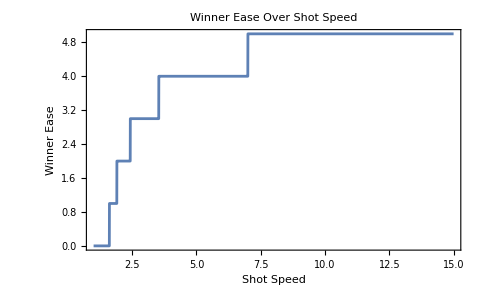

The winner ease plateaus up to the level of the court width, just like the invasion model! Let’s see it with a bunch of court widths:

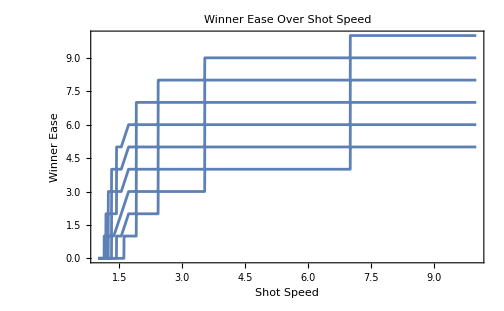

So here we’re starting to see that, at their core, net sports are also about controlling space.

### To Conclude: Livestreams, Chess, Duck-hunting and Entropy

I feel like this project is gaining momentum. Prab, one of my fellow students, said that his summer school project took him 3 weeks, but once he did it he could do it in 3 days. I was able to complete this model 5x faster than the previous one because of the similarities with the invasion sport model.

One aspect I really enjoyed was I livestreamed all 20 hours of it. This creates a sense of urgency when I’m coding and helps spend time only on the things that will move the research forward. While building this model, I also found I’m about 2x faster coder in the morning. I did the entire shot selection functionality this morning within 3 hours. I also noticed my typing speed compared to top programmers is quite slow and is something I would like to improve.

So what’s next? We’ve been doing a lot of modeling using simulation, I think it’s due time for some real world data. Now, the data we want with ball tracking and player tracking at different court sizes does not exist. We will have to get creative, looking at moments within a game, or looking at similar games with good data, like Chess and Rocket League.

For future models, this tennis model is very similar to something like duck hunting, but instead of trying to hit the ball away from the defender you are trying to hit it at him. This could be interesting to look at.

We are building towards a theory for any adversarial dynamic. The rule that’s starting to emerge is the way to win at a high level is to increase your entropy with respect to your opponent. You want to be able to move in as many places as possible and have the defense not know where you’re going. Much work is needed to analyze real-world data and continue to develop the theory. So it’s back to the trenches for me. I’ll be back with another update in a week. Thank you for reading.

## Code

### Initialization

```mathematica
initgame[width_]:= Module[{court, net, abline, hbline, astart, dstart, bstart, framerate,startpos }, 
court = Rectangle[{1, 1} - playerSize, {width, courtLength}+playerSize]; 
net = Line[{{1, (courtLength+1)/2 }, {width, (courtLength + 1) / 2}}];
abline = Subdivide[{1, courtLength}, {width, courtLength}, width -1 ];
hbline =Subdivide[{1, 1}, {width, 1}, width -1 ];
astart = First[hbline];
dstart  = First[abline];
bstart = astart;
framerate = 12;
startpos = <|"hpos"->astart, "apos"->dstart,"bpos"->bstart|>
]
```

### Helper

```mathematica
getdist[start_, dest_]:= EuclideanDistance[start, dest]
```

```mathematica
restrict[val_, {min_, max_}]:= If[val < min, min, If[val>max,max, val]];
```

```mathematica
gettime[start_, dest_, speed_, rtime_:0]:= Floor[EuclideanDistance[start, dest] / speed] - rtime;
```

```mathematica
getinfo[pos_, params_]:= Module[{homeQ, homeaway, attdef, attdefstring, blines},
homeQ= pos["bpos"][[2]] == params["hbline"][[1, 2]];
homeaway = {pos["hpos"], pos["apos"]};
attdef = If[homeQ, homeaway, Reverse@homeaway ];
attdefstring = If[homeQ, {"hpos", "apos"}, {"apos", "hpos"}];
blines = If[homeQ, {params["hbline"], params["abline"]},  Reverse@{params["hbline"], params["abline"]}];
<|"homeQ"->homeQ, 
"att"->attdef[[1]],
"def"->attdef[[2]],
"attstring"-> attdefstring[[1]],
"defstring"->attdefstring[[2]], 
"attbline"->blines[[1]],
"defbline"->blines[[2]]
|>
]
```

### Visualization

```mathematica
getPoint[center_,angle_,radius_]:=center+radius*AngleVector[angle]
```

```mathematica
getRecPoints[point_, size_]:={getPoint[point, 225Degree, size], getPoint[point, 45Degree, size]}
```

```mathematica
getTriPoints[point_, size_]:=
{getPoint[point, 88Degree, size - 1/12],getPoint[point, 210 Degree, size], getPoint[point, 330Degree, size ]}
```

```mathematica
getObjectShapes[pos_]:= 
{Rectangle@@getRecPoints[pos["hpos"], playerSize], N@Polygon@getTriPoints[pos["apos"],playerSize], 
Disk[pos["bpos"], ballSize]}
```

```mathematica
Options[show] = {"points"->{}};
show[pos_Association, OptionsPattern[{show, Graphics}]]:= Module[{hrec, atri, ball}, 
{hrec, atri, ball} = getObjectShapes[pos];
Graphics[{FaceForm@White, EdgeForm@Black,court,singleslines, net,EdgeForm@None, FaceForm@Gray, Point@N@OptionValue["points"], FaceForm@Blue, hrec,FaceForm@Red,atri, Green, ball},ImageSize->OptionValue[ImageSize]]
]
```

```mathematica
show[poss_List]:= ListAnimate[show/@ poss, DefaultDuration->Length@poss/65, AnimationRepetitions->1]
```

```mathematica
animateobj[start_, dest_List, speed_, reactiontime_:0, timespec_:-1]:=Module[{ptime, movetime, move, react, wtime, wait},
ptime = Max[gettime[start, dest, speed], 1];
movetime = If[timespec == -1, ptime+reactiontime, timespec];
move = Subdivide[start, dest, ptime*framerate];
react = Join[Table[start, reactiontime*framerate],move];
wtime =movetime*framerate;
wait = PadRight[react, wtime, {Last@react}]
]
```

```mathematica
animateshot[{pos1_, pos2_},params_]:= Module[{i1, i2, timespec, att, def, amove, dmove, bmove},
i1 = getinfo[pos1, params];
i2 = getinfo[pos2, params]; 
timespec = gettime[pos1["bpos"], pos2["bpos"], params["shotspeed"]];
att = pos1[i1["attstring"]];
def = pos1[i1["defstring"]];
amove = animateobj[i1["att"], i2["def"],params["pspeed"], swingtime, timespec];
dmove = animateobj[i1["def"], i2["att"], params["pspeed"], params["rtime"], timespec];
bmove =  animateobj[pos1["bpos"],pos2["bpos"], params["shotspeed"], 0, timespec];
MapThread[<|i1["attstring"]->#1, i1["defstring"]->#2, "bpos"->#3|>&, {amove, dmove, bmove}]
]
```

```mathematica
animatepoint[poslist_]:=Module[{pairs}, 
 pairs = Partition[poslist, 2, 1];
Flatten[animateshot[#, params]&/@ pairs, 1]
]
```

### Evaluation

```mathematica
winnerQ[pos_, dest_,info_, params_]:= Module[{ddist, bdist, dtime, btime},
ddist = EuclideanDistance[dest,info["def"]];
bdist =  EuclideanDistance[dest,pos["bpos"]];
dtime =  ddist+params["rtime"]/params["pspeed"];
btime = bdist / params["shotspeed"];
btime < dtime
]
```

```mathematica
getwinnerease[params_]:= Module[{dests},
dests = Table[{i, courtLength}, {i, params["cwidth"]}];
Count[winnerQ[initgame[params["cwidth"]], #, params]&/@dests, True]
]
```

```mathematica
getwinnercount[pos_, params_]:= Module[{info, shots, qs}, 
info = getinfo[pos, params];
shots = info["defbline"];
qs =winnerQ[pos, #,info, params]&/@shots;
Count[qs, True]
]
```

```mathematica
result[pos_, params_]:=Module[{linestring,win, def, team,  line, in, ball},
ball = pos["bpos"];
{linestring, win, def} = If[ball[[2]]== params["hbline"][[1, 2]],{"hbline", 1, pos["hpos"]},  {"abline", 1, pos["apos"]}];
line =  params[linestring];
in = params[linestring<>"in"];
Which[
MemberQ[in, ball] && ball!= def, win, 
!MemberQ[in, ball], -win,
True, 0
]]
```

### Game Logic

```mathematica
movedefender[pos_,info_, params_, bdest_ ]:= Module[{bdist,pdisp, dir, time, disp, moveX},
bdist = EuclideanDistance[bdest, pos["bpos"]];
pdisp = First@bdest- First@info["def"];
dir = Sign[pdisp];
time = Floor[bdist / params["shotspeed"]] - params["rtime"];
disp = dir*(Min[Floor[params["pspeed"]*time], Abs@pdisp]);
moveX =restrict[First@info["def"]+disp, {First@First@params["ablinein"], First@Last@params["ablinein"]}];
{moveX, info["def"][[2]]}
]
```

```mathematica
aimshot[pos_,info_, params_]:= Module[{linein, agg, acc, sideX, shots, shotsX},
linein = If[pos["bpos"][[2]] ==  params["hbline"][[1, 2]],params["ablinein"], params["hblinein"]];
agg = params["aggression"];
acc = params["accuracy"];
sideX =RandomChoice@{First@linein[[1]]+agg, First@linein[[-1]] - agg} ;
shotsX = Range[Max[sideX - acc, 1], Min[sideX + acc, params["cwidth"]], 1];
shots = {#, linein[[1, 2]]}&/@ shotsX;
shots
]
```

```mathematica
recover[pos_,info_, params_, dest_]:= Module[{shottime, recdist,moveXs, moves,moveposlist, bestpos},
shottime = gettime[pos["bpos"], dest, params["shotspeed"], swingtime];
recdist = shottime*params["pspeed"];
moveXs = Range[Max[First@info["att"] - recdist, 1], Min[First@info["att"] + recdist, params["cwidth"]], 1];
moves = Thread[{#, info["att"][[2]]}&[moveXs]];
moveposlist =<|info["attstring"]->#,"bpos"->dest, info["defstring"]->dest|>&/@moves;
wcs =  getwinnercount[#, params]&/@ moveposlist;
(*Echo@wcs;*)
bestpos = First@MinimalBy[moveposlist, getwinnercount[#, params]&,  1];
bestpos[info["attstring"]]
]
```

```mathematica
hit[pos_, params_]:= Module[{info,shots,  dest, newd, recatt},
info = getinfo[pos, params];
shots =aimshot[pos,info, params] ;
dest = RandomChoice@shots;
(*Echo@winnerQ[pos, dest, info, params];*)
newd = movedefender[pos,info, params,dest];
recatt = recover[pos, info, params, dest];
<|info["attstring"]->recatt, info["defstring"]->newd, "bpos"->dest|>
]
```

```mathematica
playpoint[pos_, params_, max_:5]:= NestWhileList[hit[#,params]&,pos, result[#, params]== 0&,1, max]
```

```mathematica
ClearAll@recover
```

### Gameplay

```mathematica
Column[p = playpoint[startpos, params, 10]];
```

```mathematica
ap = animatepoint[p];
```

```mathematica
show@ap
```

### Constants

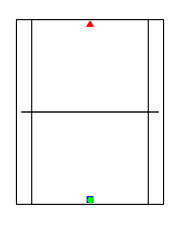

```mathematica
courtLength = 24;
courtWidth  =19;
out = 2;
playerSize = 12/courtWidth;
ballSize = 8/courtWidth;
court = Rectangle[{1, 1} - playerSize, {courtWidth, courtLength}+playerSize]; 
singleslines = Rectangle[{1+out, 1} - playerSize, {courtWidth-out, courtLength}+playerSize]; 
net = Line[{{1, (courtLength+1)/2 }, {courtWidth, (courtLength + 1) / 2}}];
abline = Subdivide[{1, courtLength}, {courtWidth, courtLength}, courtWidth -1 ];
hbline =Subdivide[{1, 1}, {courtWidth, 1}, courtWidth -1 ];
hblinein = ArrayPad[hbline, {-out}];
ablinein = ArrayPad[abline, {-out}];
astart = Median[hbline];
dstart  = Median[abline];
bstart = astart;
framerate = 4;
startpos = <|"hpos"->astart, "apos"->dstart,"bpos"->bstart|>;
info = getinfo[startpos];
show[startpos, ImageSize->Small]
swingtime = 1;
```

### Parameters

```mathematica
params = <|
"cwidth"->  courtWidth,
"abline"->abline,
"hbline"->hbline,
"ablinein"->ablinein,
"hblinein"->hblinein,
"shotspeed"->  4,
"pspeed"->  1,
"rtime"->  0,
"accuracy"->2,
"aggression" ->2
|>;
```

## Acknowledgments

Thank you to Brad Klee for giving me the tennis idea. Thank you to my mentors Eric and John for encouraging me. Thanks to WSS students for being cool.

## Cite This Notebook

“Universal Laws Of Sports: Continued”
by Willem Nielsen
https://community.wolfram.com/groups/-/m/t/3232331?p_p_auth=kVoCQ60I